# SIRS does not have Hopf bifurcation

by  F. Avram and R. Adenane

ABSTRACT (original article): 
Keywords: 

 CITATION (original article):

## Constants definition and analysis of the SIRS case with γs=0 and γs>0 proving absence of Hopf:

In this first cell,  we explore a specific SIRS model configuration that inherently precludes the occurrence of Hopf bifurcations.
We begin by formulating the generalized SIRS model with the inclusion of parameters that govern the demography and the rates of infection, recovery,   and loss of immunity. Through the analysis of the characteristic polynomial  at the unique endemic point, and by using the Routh-Hurwitz criteria for the stability, we covered the case of absence of Hopf bifurcation when the vaccination rate is excluded; here the command reduce takes only 1 second of execution.
The analysis presented in this first cell is realized in the linear case of vaccination which is γs s, and it could be also presented in the constant vaccination rate case by putting the condition cctvac into the RHS function.

```mathematica
ClearAll["Global‘*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession, NotebookAutoSave -> True];
NotebookSave[];<<EpidCRN.wl;(*Names["EpidCRN`*"]*)
Format[γr]:=Subscript[γ,r];Format[μi]:=Subscript[μ,i];Format[γs]:=Subscript[γ,s];

cgr=γr->0;cgs=γs->0;cgrs={γr->0,γs->0,λ->μ};cmi=μi->μ;
clinvac=rs->γs s;cctvac=rs->γs;

sd=(λ (γr+μ))/(μ (γr+γs+μ));R0=sd β/(γ+μi);

(*Generalized SIRS example*)
S={{1,-1,0,1,-1,-1,0,0},
          {0,1,-1,0,0,0,-1,0},
          {0,0,1,-1,1,0,0,-1}};
Vg={λ ,β s i ,γ i,γr r,rs,s  μ, i μi ,r  μ};
RHS=S.Vg/.clinvac;
var={s,i,r};par=Par[RHS,var];cp=Thread[par>0];
cp[[4]]=γs>=0;cp
cv=Thread[var>=0];ct={cp,cv}//Union//Flatten;

Print["SIRS model with  vaccination has RHS=",RHS//MatrixForm," has S= ",S//MatrixForm," and ", par//Length,
" par which are", par]
 Print["Check sum ",Total[RHS]//FullSimplify," reveals N=s+i+r is conserved when μi=μ, N0=λ/μ"]
 so=Solve[RHS==0,var];
mod={RHS,var,par};

Print["RHS has ",Length[so], " fixed points",so//FullSimplify]
inf={2};
cdfe=Append[DFE[mod,inf][[1]],var[[inf]][[1]]->0];

jac=Grad[RHS,var];
Print["jac (not cooperative) is",jac//MatrixForm]
jaD=jac/.so[[1]];ei=Eigenvalues[jaD]//FullSimplify;
Print["Eigenvalues at DFE are",ei," R0 = ",R0]


jaE=jac/.so[[2]];
{co,h3,ine}=Hur3M[jaE]//Simplify;
Print["charpol at E_1, factored,  has coeffs",co]
Timing[re=Reduce[Append[Join[cp,ine],h3>0]/.cgs//FullSimplify];]
Print["the RouthHur stability condition for E_1 is ", re," or R0>1, so SIRS  does not have Hopf 
bifurcation when gamma_s=0"]
```

{β>0,γ>0,γ_r>0,γ_s≥0,λ>0,μ>0,μ_i>0}

SIRS model with  vaccination has RHS=(-i s β+r γ_r-s γ_s+λ-s μ
i s β-i γ-i μ_i
i γ-r γ_r+s γ_s-r μ) has S= (1 | -1 | 0 | 1 | -1 | -1 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | -1 | 0
0 | 0 | 1 | -1 | 1 | 0 | 0 | -1) and 7 par which are{β,γ,γ_r,γ_s,λ,μ,μ_i}

Check sum λ-(r+s) μ-i μ_i reveals N=s+i+r is conserved when μi=μ, N0=λ/μ

RHS has 2 fixed points{{s→(λ (γ_r+μ))/(μ (γ_r+γ_s+μ)),i→0,r→(γ_s λ)/(μ (γ_r+γ_s+μ))},{s→(γ+μ_i)/β,i→(β λ (γ_r+μ)-μ (γ_r+γ_s+μ) (γ+μ_i))/(β γ μ+β (γ_r+μ) μ_i),r→(β γ λ-(γ+μ_i) (γ μ-γ_s μ_i))/(β γ μ+β (γ_r+μ) μ_i)}}

jac (not cooperative) is(-i β-γ_s-μ | -s β | γ_r
i β | s β-γ-μ_i | 0
γ_s | γ | -γ_r-μ)

Eigenvalues at DFE are{-μ,-γ_r-γ_s-μ,-γ+(β λ (γ_r+μ))/(μ (γ_r+γ_s+μ))-μ_i} R0 = (β λ (γ_r+μ))/(μ (γ_r+γ_s+μ) (γ+μ_i))

charpol at E_1, factored,  has coeffs{β λ (γ_r+μ)-μ (γ_r+γ_s+μ) (γ+μ_i),(β λ (γ_r+μ) (γ+γ_r+μ+μ_i)-μ (γ_r+γ_s+μ) (γ^2+μ_i^2+γ (γ_r+2 μ_i)))/(γ μ+(γ_r+μ) μ_i),(γ μ^2+β λ (γ_r+μ)+(γ_r^2+γ_r γ_s+2 γ_r μ+μ^2) μ_i)/(γ μ+(γ_r+μ) μ_i),1}

{1.10938,Null}

the RouthHur stability condition for E_1 is μ>0&&γ_r>0&&μ_i>0&&γ>0&&λ>0&&β>(γ μ+μ μ_i)/λ or R0>1, so SIRS  does not have Hopf 
bifurcation when gamma_s=0

Then, we check in the general case of SIRS when the vaccination rate is included, and we also found that Hopf bifurcation doesn’t occur in that case as well, where this time the command Reduce takes 338 seconds.

```mathematica
Timing[re=Reduce[Append[Join[cp,ine],h3>0]//FullSimplify];]
Print["the RouthHur stability condition for E_1 is ", re," or R0>1, so SIRS  does not have Hopf 
bifurcation when gamma_s>0"]
```

{111.,Null}

the RouthHur stability condition for E_1 is μ>0&&γ_r>0&&μ_i>0&&γ>0&&γ_s≥0&&λ>0&&β>(γ γ_r μ+γ γ_s μ+γ μ^2+γ_r μ μ_i+γ_s μ μ_i+μ^2 μ_i)/(γ_r λ+λ μ) or R0>1, so SIRS  does not have Hopf 
bifurcation when gamma_s>0

```mathematica
Timing[re=Reduce[Append[Join[cp,ine],h3==0&&R0>1]//FullSimplify];]
Print["the RouthHur Hopf condition for E_1 is ", re,"  so SIRS  does not have Hopf 
bifurcation when gamma_s>0"]
```

{89.5,Null}

the RouthHur Hopf condition for E_1 is False  so SIRS  does not have Hopf 
bifurcation when gamma_s>0

The Reactions representing the SIRS allow computing CRN theoretical quantities like the deficiency, which is 1

ReactionKinetics Version 1.0 [March 25, 2018] using Mathematica Version 13.3.1 for Microsoft Windows (64-bit) (July 24, 2023) (Version 13.3, Release 1) loaded 13 September 2024 at 23:11 TimeZone
GNU General Public License (GPLv3) Terms Apply.

Please report any issues, comments, complaint related to ReactionKinetics at
[jtoth@math.bme.hu](mailto:jtoth@math.bme.hu), [nagyal@math.bme.hu](mailto:nagyal@math.bme.hu) or [dpapp@iems.northwestern.edu](mailto:dpapp@iems.northwestern.edu)

{0→S,I+S→2 I,I→R,R→S,S→R,S→0,I→0,R→0}

Stoichio mat(1 | -1 | 0 | 1 | -1 | -1 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | -1 | 0
0 | 0 | 1 | -1 | 1 | 0 | 0 | -1) has rank 3 and deficiency δ=N-L-S=6-2-3=1

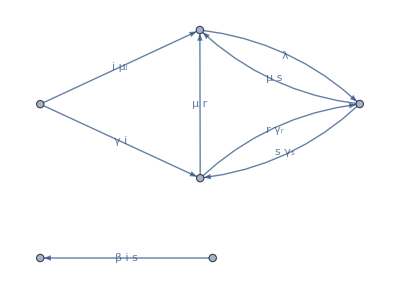

```mathematica
Needs["ReactionKinetics`"];
(*Names["ReactionKinetics`*"];
Models["ReactionKinetics`*"];*)
ReactionsData["Properties"];
(*Generalized SIRS as a CRN*)
RN={0->"S","S"+"I"->2 "I","I"->"R","R"->"S","S"->"R","S"->0,"I"->0,"R"->0}
RND=ReactionsData[RN];
S= RND["γ"];
Print["Stoichio mat",S//MatrixForm, " has rank ",MatrixRank[S]," and deficiency ", RND["deficiency"]]
expo= RND["α"]//Normal//Transpose;
var={s,i,r};tk={λ,β,γ, γr,γs, μ, μi,μ};

rv=expM[var,expo];
Rv=tk*rv;
ShowFHJGraph[RN,Rv,DirectedEdges->True,VertexLabeling->RND["complexes"],ImageSize->400(*,StronglyConnectedComponentsColors->{Pink}*)]
```

```mathematica
gr=GroebnerBasis[RHS,{i}]//Factor
gr//Length
Solve[gr[[3,3]]==0,s]
```

{(γ_s λ-r γ_r μ-r γ_s μ-r μ^2) (β γ λ-r β γ μ-γ^2 μ-r β γ_r μ_i+γ γ_s μ_i-r β μ μ_i-γ μ μ_i+γ_s μ_i^2),γ λ-r γ μ-s γ μ-r γ_r μ_i+s γ_s μ_i-r μ μ_i,-((γ_s λ-r γ_r μ-r γ_s μ-r μ^2) (s β-γ-μ_i)),(-λ+r μ+s μ) (s β-γ-μ_i),-r s β γ_r+r γ γ_r+s^2 β γ_s-s γ γ_s+γ λ-r s β μ-s γ μ,-λ+r μ+s μ+i μ_i,i γ-r γ_r+s γ_s-r μ,i s β-r γ_r+s γ_s-λ+s μ}

8

{{s→(γ+μ_i)/β}}

```mathematica
GroebnerBasis[RHS[[2]],{i}]//Factor
```

{i (s β-γ-μ_i)}

δ=N-L-S=7-2-3=2

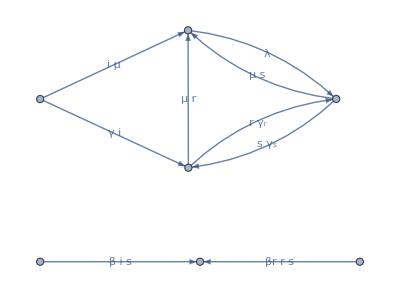

```mathematica
ReactionsData["Properties"];
RN1={0->"S","S"+"I"->2 "I","S"+"R"->2"I","I"->"R","R"->"S","S"->"R","S"->0,"I"->0,"R"->0};
RND1=ReactionsData[RN1];
RND1["deficiency"]
expo1= RND1["α"]//Normal//Transpose;
var1={s,i,r};tk1={λ,β,βr,γ, γr,γs, μ, μ,μ};

rv1=expM[var1,expo1];
Rv1=tk1*rv1;
ShowFHJGraph[RN1,Rv1,DirectedEdges->True,VertexLabeling->RND1["complexes"],ImageSize->400(*,StronglyConnectedComponentsColors->{Pink}*)]
```

δ=N-L-S=7-2-3=2

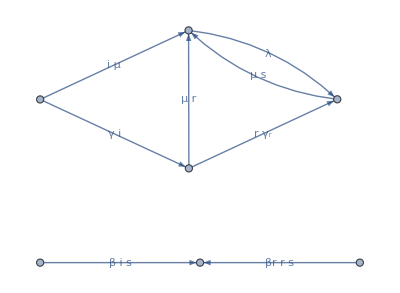

```mathematica
ReactionsData["Properties"];
RN2={0->"S","S"+"I"->2 "I","S"+"R"->2"I","I"->"R","R"->"S","S"->0,"I"->0,"R"->0};
RND2=ReactionsData[RN2];
RND2["deficiency"]
expo2= RND2["α"]//Normal//Transpose;
var2={s,i,r};tk2={λ,β,βr,γ, γr, μ, μ,μ};

rv2=expM[var2,expo2];
Rv2=tk2*rv2;
ShowFHJGraph[RN2,Rv2,DirectedEdges->True,VertexLabeling->RND2["complexes"],ImageSize->400(*,StronglyConnectedComponentsColors->{Pink}*)]
```